Setup plotting functions to show us the 1D dispersion. Because Plot3D & ContourPlot also accept lists of functions, this also allow us to plot multiple bands later on.

```mathematica
PlotDispersion1D[Disp_, OptionsPattern[{Levels -> 5, Title -> None, Points -> 100}]] :=
Plot[Disp, {k, -π, π}, ColorFunction-> "BlueGreenYellow",
			PlotLabel -> OptionValue["Title"], PlotLegends -> Automatic, AxesLabel -> {k, ϵ[k]},
			PlotPoints -> OptionValue["Points"]]
PlotDispersion2D[Disp_, OptionsPattern[{Levels -> 5, Title -> None, Points -> 100}]] :=
Plot3D[Disp, {Subscript[k, x], -π, π}, {Subscript[k, y], -π, π}, MeshFunctions-> {#3 &}, ColorFunction-> "BlueGreenYellow",
			PlotLabel -> OptionValue["Title"], PlotLegends -> Automatic, Mesh -> OptionValue["Levels"],
			PlotPoints -> OptionValue["Points"], PlotStyle -> Opacity[.7]]
PlotDispersion2DContour[Disp_, OptionsPattern[100{Levels -> 5, Title -> None}]] :=
ContourPlot[Disp, {Subscript[k, x], -π, π}, {Subscript[k, y], -π, π},
			PlotLabel -> OptionValue["Title"], PlotLegends -> Automatic, Contours -> OptionValue["Levels"]]
```

In general in can be shown that given hopping integrals t_kl^ij and corresponding overlaps s_kl^ij, where i/j specifies interaction/overlap between the ith & jth orbital in the basis and (kl) gives the crystallographic direction/distance between interacting unit cells the band dispersions are solutions to the eigenvalue problem

det(H - E_kS) = 0,

where H_ij is the discrete fourier transform of all t_kl^ij and mutatis mutandis for S_ij. If the hopping is inversion symmetric then this is equivalent to a discrete cosine transform. In the single band case this simplifies to

E_k= H/S.

To generalize to 3D or recover the 1D case, simply replace the directions (kl) with (hkl) or (k).

```mathematica
CosTransform[basis_, kvector_] := CosTransform[basis, kvector, #1, #2] &;
CosTransform[basis_, kvector_, E0_, hopMap_] := E0 + Plus @@
KeyValueMap[∑_(i = 1)^Length[#2] 2  #2⟦i⟧Cos[i*(basis . #1) . kvector] &] @ hopMap;
ExpTransform[basis_, kvector_] := ExpTransform[basis, kvector, #1, #2] &;
ExpTransform[basis_, kvector_, E0_, hopMap_] := E0 + Plus @@
KeyValueMap[∑_(i = 1)^Length[#2] 2  #2⟦i⟧Exp[I * i*(basis . #1) . kvector] &] @ hopMap;
(* 
Mathematica's Conjugate makes simplying expressions all kinds of weird, so we use a cheap trick for exponentials (the only thing we're interested in).
With this you can use A^† as the complex conjugate of A.
*)
SuperDagger[expr_] := expr /. {k -> -k, Subscript[k, x] -> -Subscript[k, x], Subscript[k, y]-> -Subscript[k, y]};
Dispersion[H_, S_] := Eigenvalues[{H, S}];
```

To construct the TB Hamiltonian for your system, first build the H_ij/S_ij with the CosTransform or ExpTransform. Use former if your problem is inversion symmetric and the latter in the general case. In any case H_ij=H_ji* ∧ S_ij=S_ji* has to hold. 
The first argument is your real space basis matrix. If you play with this, be aware that the plotting functions only sample k-space in the interval [-π, π], so changing the basis will change how much of the first Brillouin zone you get to see in the these plots.
The second argument should give a general k vector, this tells the transforms how many dimensions you want to transform in. So use {k} for a 1D case or {k1, k2, k3} for a 3D case. (Note that the PlotDispersion1D and PlotDispersion2D functions expect {k} and {k_x, k_y}  respectively). You could also use this to transform your k-space to a different basis, e.g. by just multiplying the k vector by 2 to also plot the second Brillouin zone.
The third argument only makes sense for the H_ii terms and gives the original ground level energy of the ith orbital, leave it as zero otherwise.
The last, most complicated argument then gives the actual hopping or overlap terms. It should be a mapping from from crystallographic directions to a list of hopping terms in that direction. So in a 1D case this could be <| {1} → {1., .5} |> to specify hopping to the nearest and next-nearest lattice cell in (1) direction (the only one in 1D). The pointy bits are Mathematica syntax for a mapping and the arrow points from the key (the direction) to the value (the hopping list). In general it should look like <|{h,k,l} → {t_hkl, t_(2h,2k,2l), etc.} |>. It should become a lot clearer with the examples below.
Additionally you can also call both transforms with only the two former arguments only to get a function that only takes the latter two arguments.

For a simple example let’s consider a 1D chain of atoms, where each atom only contributes only one orbital. We’ll also neglect overlap. That means t_1 = -1, ∀_(n > 1)t_n=0 and S = {{1}} (H, S still have to be input as matrices even if they’re just 1x1).
In 1D the basis matrix is just the lattice constant.

{1-2 Cos[k]}

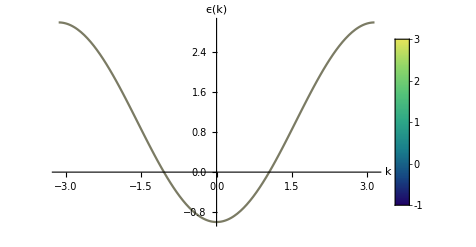

```mathematica
basis1D = {{1}};
CT1D = CosTransform[basis1D, {k}];
Disp1DSingle = Dispersion[{{CT1D[1, <| {1} -> {-1} |>]}},{{ 1}}]
PlotDispersion1D[Disp1DSingle]
```

We can now add a second orbital per unit cell, whether this corresponds a dimer chain or a second orbital on the single atom, is a question of interpreting the hopping integrals. Note the nice hybridization gap opening between the otherwise unperturbed cosine bands.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.1 (-22. Cos[k]-1.41421 √(83.+81. Cos[2. k])),0.1 (-22. Cos[k]+1.41421 √(83.+81. Cos[2. k]))}

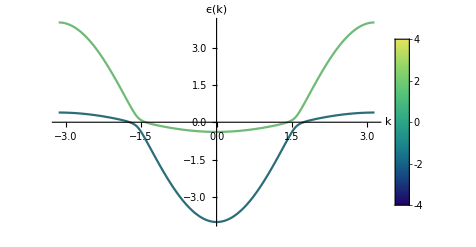

```mathematica
Disp1DDouble = Dispersion[
{{CT1D[0, <| {1} -> {-2} |>], .2},
{.2, CT1D[0, <| {1} -> {-.2} |>]}},
{{1, 0},
{0, 1}}]
PlotDispersion1D[Disp1DDouble]
```

In  the last case the two orbits had the same ground state energy, zero, but we can also shift them against each other.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.1 (10.-22. Cos[k]-1.41421 √(133.+180. Cos[k]+81. Cos[2. k])),0.1 (10.-22. Cos[k]+1.41421 √(133.+180. Cos[k]+81. Cos[2. k]))}

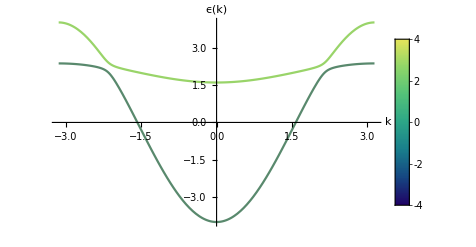

```mathematica
Disp1DDoubleShifted = Dispersion[
{{CT1D[0, <| {1} -> {-2} |>], .2},
{.2, CT1D[2, <| {1} -> {-.2} |>]}},
{{1, 0},
{0, 1}}]
PlotDispersion1D[Disp1DDoubleShifted]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.1 (25.-22. Cos[k]-1. √(791.+900. Cos[k]+162. Cos[2. k])),0.1 (25.-22. Cos[k]+√(791.+900. Cos[k]+162. Cos[2. k]))}

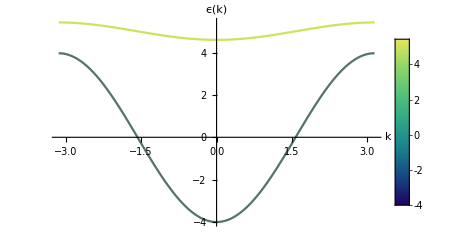

```mathematica
Disp1DDoubleSeparated = Dispersion[
{{CT1D[0, <| {1} -> {-2} |>], .2},
{.2, CT1D[5, <| {1} -> {-.2} |>]}},
{{1, 0},
{0, 1}}]
PlotDispersion1D[Disp1DDoubleSeparated]
```

Moving to 2D crystals.

```mathematica
squareBasis = {{1, 0},
	     	    {0, 1}};
CTSquare = CosTransform[squareBasis, {Subscript[k, x], Subscript[k, y]}];
DispSquare = Dispersion[{{CTSquare[1, <| {0, 1} -> {-2}, {1, 0} -> {-2} |>], -.5},
					{-.5, CTSquare[1, <| {0, 1} -> {-.5}, {1, 0} -> {-.5} |>]}}, {{1, 0}, {0, 1}}]
PlotDispersion2D[DispSquare]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.5 (2.-5. Cos[k_x]-5. Cos[k_y]-0.707107 √(20.+9. Cos[2. k_x]+18. Cos[k_x-1. k_y]+9. Cos[2. k_y]+18. Cos[k_x+k_y])),0.5 (2.-5. Cos[k_x]-5. Cos[k_y]+0.707107 √(20.+9. Cos[2. k_x]+18. Cos[k_x-1. k_y]+9. Cos[2. k_y]+18. Cos[k_x+k_y]))}

-Graphics3D-

What about graphene? Since Graphene is not inversion-symmetric (with the unit cell chosen below), we have to use the discrete fourier transform here, but as we that the result has to be real we can convert back to cosines after the calculated the bands using ExpToTrig.
In the simplest description we can just assume that there is one orbital at each C atom that interacts only with the three nearest other C atoms. As the interacting atoms are not symmetry equivalent, in the formalism above we have a 2x2 matrix where only the off-diagonals are interesting. The diagonals have to be constant and hence only shift the energy scale.

```mathematica
hexBasis = Transpose @ {{3, √3}, {3, -√3}} / 2 ;
hexBasis // MatrixForm
CTGraph = ExpTransform[hexBasis, {Subscript[k, x],Subscript[k, y]}];
DispGraphene = ExpToTrig /@ Dispersion[{{1, CTGraph[0, <| {0, 0} -> {1}, {0, 1}  -> {1} , {1, 0} -> {1}|>]},
						{CTGraph[0, <| {0, 0} -> {1}, {0, -1}  -> {1}, {-1, 0} -> {1}|>], 1}}, IdentityMatrix[2]]
PlotDispersion2D[DispGraphene]
```

(3/2 | 3/2
(√3)/2 | -(√3)/2)

{1-2 √(3+2 Cos[√3 k_y]+2 Cos[(3 k_x)/2-(√3 k_y)/2]+2 Cos[(3 k_x)/2+(√3 k_y)/2]),1+2 √(3+2 Cos[√3 k_y]+2 Cos[(3 k_x)/2-(√3 k_y)/2]+2 Cos[(3 k_x)/2+(√3 k_y)/2])}

-Graphics3D-

Once we have the dispersion relations we can try to compute the density of states by evenly sampling the dispersion and plot a histogram from that. The functions below plot the probability density functions so that increasing the sample number only increases accuracy. Of course physically the number of samples is given by the number of unit cells in the system and you have to multiply by the total number of states.

```mathematica
DOS1D[Disp_, OptionsPattern[{Samples -> 1000, Bins -> 50, Title -> None}]]:= Histogram[Flatten @ Table[Disp, {k, -π, π, 2π/OptionValue["Samples"]}], 
OptionValue["Bins"], "PDF", AxesLabel -> {"E"}, PlotLabel -> OptionValue["Title"]];
DOS2D[Disp_, OptionsPattern[{Samples -> 1000, Bins -> 50, Title -> None}]] := Histogram[Flatten @ Table[Disp, 
{Subscript[k, x], -π, π, 2π/OptionValue["Samples"]}, {Subscript[k, y], -π, π, 2π/OptionValue["Samples"]}], 
OptionValue["Bins"], "PDF", AxesLabel -> {"E"}, PlotLabel -> OptionValue["Title"]];
```

Here are plots for the 1D system show cased so far. It’s nice to see that even with the hybridization we’ve seen above, in terms of DOS, bands just add up, roughly speaking.

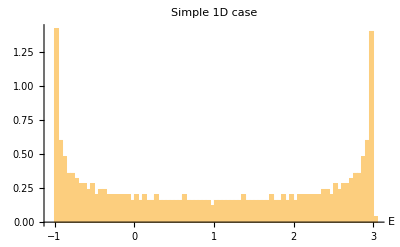

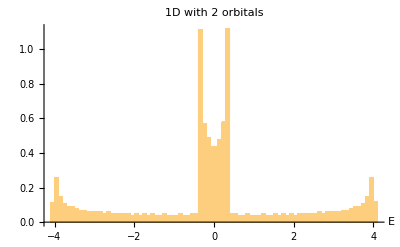

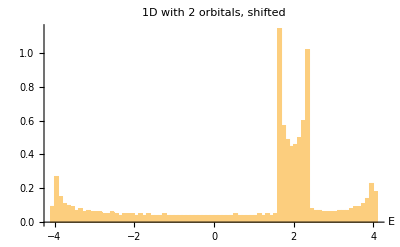

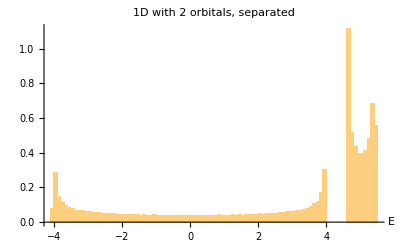

```mathematica
DOS1D[Disp1DSingle, Bins -> 100, Title -> "Simple 1D case"]
DOS1D[Disp1DDouble, Bins -> 100, Title -> "1D with 2 orbitals"]
DOS1D[Disp1DDoubleShifted, Bins -> 100, Title -> "1D with 2 orbitals, shifted"]
DOS1D[Disp1DDoubleSeparated, Samples -> 2000, Bins -> 100, Title -> "1D with 2 orbitals, separated"]
```

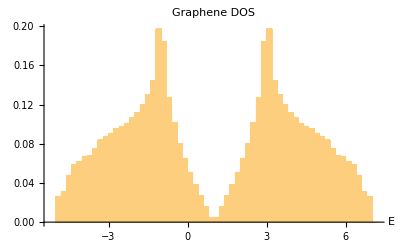

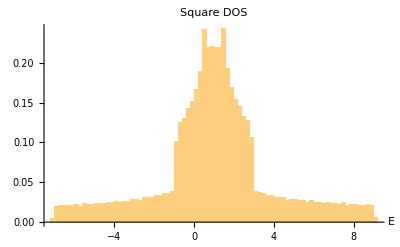

```mathematica
DOS2D[DispGraphene, Samples -> 200, Bins -> 80, Title -> "Graphene DOS"]
DOS2D[DispSquare, Samples -> 200, Bins -> 80, Title -> "Square DOS"]
```